# Zad 1

{x→-0.267949,y→0.}

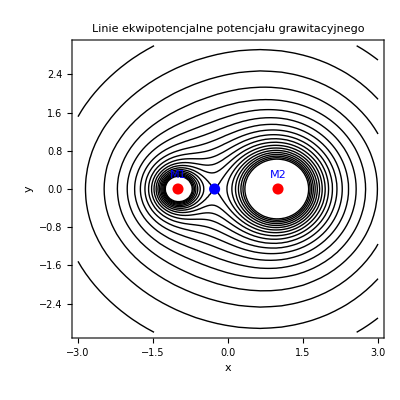

```mathematica
(*1. Definicja potencjału*)
Phi[x_,y_,M1_,M2_,a_]:=-M1/Sqrt[(x+a)^2+y^2]-M2/Sqrt[(x-a)^2+y^2]

(*Parametry do podpunktu 2 i 3*)
m1Val=1;
m2Val=3;
aVal=1;

(*3. Znalezienie punktu stacjonarnego (numerycznie)*)
(*Szukamy punktu (x,y),w którym pochodne cząstkowe (gradient) są równe 0.*)
(*Z fizycznego punktu widzenia punkt równowagi leży na osi łączącej masy.*)
(*Ponieważ M2>M1,punkt powinien być bliżej lżejszej masy M1 (czyli bliżej-1).*)

stacjonarny=FindRoot[{D[Phi[x,y,m1Val,m2Val,aVal],x]==0,D[Phi[x,y,m1Val,m2Val,aVal],y]==0},{{x,0},{y,0}} (*Punkt startowy poszukiwań*)]

(*2. Rysowanie linii ekwipotencjalnych*)
wykresPotencjal=ContourPlot[Phi[x,y,m1Val,m2Val,aVal],{x,-3,3},{y,-3,3},Contours->20,(*Liczba poziomic*) ContourShading->None,(*Brak wypełnienia między liniami*)Frame->True,FrameLabel->{"x","y"},PlotLabel->"Linie ekwipotencjalne potencjału grawitacyjnego",Epilog->{(*Masy jako czerwone punkty*)Red,PointSize[0.02],Point[{{-aVal,0},{aVal,0}}],(*Punkt stacjonarny jako niebieski punkt*)Blue,PointSize[0.02],Point[{x,y}/. stacjonarny],Text["M1",{-aVal,0.3}],Text["M2",{aVal,0.3}]}]

(*4 Funkcja Manipulate*)
(*Pozwala zmieniać masy i odległość suwakami*) Manipulate[Module[{sol},(*Szukamy punktu na bieżąco dla dynamicznych parametrów*)(*Quiet wycisza komunikaty o zbieżności przy szybkich zmianach*)sol=Quiet[FindRoot[{D[Phi[x,y,m1,m2,aParam],x]==0,D[Phi[x,y,m1,m2,aParam],y]==0},{{x,0},{y,0}}]];
ContourPlot[Phi[x,y,m1,m2,aParam],{x,-5,5},{y,-5,5},Contours->15,ContourShading->None,Frame->True,PerformanceGoal->"Quality",Epilog->{Red,PointSize[0.02],Point[{{-aParam,0},{aParam,0}}],Blue,PointSize[0.02],Point[{x,y}/. sol]},PlotRange->{{-5,5},{-5,5}}]],{{m1,1,"Masa M1"},0.1,10},{{m2,3,"Masa M2"},0.1,10},{{aParam,1,"Odległość a"},0.5,4}]
```

# Zad 2

b Cos[t]-(a+b t) Sin[t]

(a+b t) Cos[t]+b Sin[t]

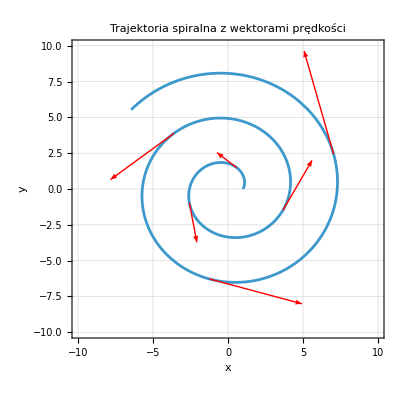

√(a^2+2 a b t+b^2 (1+t^2))

71.7778

```mathematica
(*---Zadanie 2---*)
(*1. Definicja funkcji współrzędnych*)

x[t_]:=(a+b*t)*Cos[t]
y[t_]:=(a+b*t)*Sin[t]

(*Parametry*)
aPar=1;
bPar=0.5;
tMax=15;

(*3. Analityczne składowe wektora prędkości*)
vx[t_]=D[x[t],t]
vy[t_]=D[y[t],t]

(*4. Przygotowanie wektorów prędkości do wykresu*)
czasy={1.2,3.5,5.9,8.6,10.8,12.9};

(*Lista obiektów graficznych Arrow*)
(*Każda strzałka:{Początek,Koniec}={{x(t),y(t)},{x(t)+vx(t),y(t)+vy(t)}}*)
(*Podstawiamy wartości parametrów aPar i bPar*)
wektory=Table[{Red,Arrow[{{x[t],y[t]},{x[t]+vx[t],y[t]+vy[t]}}]}/. {a->aPar,b->bPar},{t,czasy}];

(*2. Rysowanie trajektorii i naniesienie wektorów*)
trajektoria=ParametricPlot[{x[t],y[t]}/. {a->aPar,b->bPar},{t,0,tMax},PlotRange->{{-10,10},{-10,10}},(*Wymagany zakres*)Frame->True,GridLines->Automatic,FrameLabel->{"x","y"},PlotLabel->"Trajektoria spiralna z wektorami prędkości"];

(*Łączymy wykres trajektorii z wektorami*)
Show[trajektoria,Graphics[wektory]]

(*5. Obliczanie drogi*)
(*Całka z modułu prędkości*)
modulPredkosci[t_]=Sqrt[vx[t]^2+vy[t]^2]//Simplify

(*Obliczenie numeryczne (NIntegrate) dla konkretnych parametrów*)
droga=NIntegrate[modulPredkosci[t]/. {a->aPar,b->bPar},{t,0,tMax}]
```